```mathematica
sp = SequencePredict[{
{"p", "r"},
{"s", "r", "s"},
{"r", "s", "p"},
{"r", "s"}}]
```

SequencePredictorFunction[…]

```mathematica
sp[{"r", "s"}]
```

r

```mathematica
sp[{"r", "s"}, "Probabilities"]
```

<|r→0.422177,p→0.370295,s→0.207528|>

```mathematica
sp[{"r", "s"}, "RandomNextElement"]
```

r

```mathematica
sp[{"r", "s"}, "RandomNextElement"]
```

p

```mathematica
sp[{{"s", "p"}, {"r", "p"}}]
```

{r,r}

```mathematica
sp[{"r", "s"}, "NextSequence"->2]
```

{p,r}

```mathematica
sp[{{"r", "s", "r", "r"}, {"r", "s", "p", "r"}}, "SequenceProbability"]
```

{0.0117689,0.0160178}

```mathematica
sp = SequencePredict[{"the cat is grey", "my cat is fast", "this dog is scary", "the big dog", "what a lovely cat", "this is not a dog"}]
```

SequencePredictorFunction[…]

```mathematica
sp["the ca"]
```

t

```mathematica
sp["the ca", "NextElement"->4]
```

t is

```mathematica
sp["the ca", "Probabilities"]
```

<| →0.177784,a→0.0311674,b→0.0134724,c→0.0178961,d→0.0134724,e→0.0223199,f→0.0134724,g→0.0223199,h→0.0178961,i→0.0223199,l→0.0178961,m→0.0134724,n→0.0134724,o→0.0223199,r→0.0823567,s→0.0867804,t→0.35347,v→0.0134724,w→0.0134724,y→0.0311674|>

```mathematica
sp = SequencePredict[WordList[]]
```

SequencePredictorFunction[…]

```mathematica
sp["ab"]
```

l

```mathematica
markedWords = "|" <> # <>"|"&/@WordList[];
sp = SequencePredictp[markedWords]
```

SequencePredictp[{|a|,|aah|,|aardvark|,|aback|,|abacus|,|abaft|,|abalone|,|abandon|,|abandoned|,|abandonment|,|abase|,|abasement|,40103,|zoological|,|zoologist|,|zoology|,|zoom|,|zoophyte|,|zounds|,|zucchini|,|zwieback|,|zydeco|,|zygote|,|zygotic|,|zymurgy|}]
 |  |  |  |

```mathematica
markedWords = "|" <> # <>"|"&/@WordList[];
sp = SequencePredict[markedWords]
```

SequencePredictorFunction[…]

```mathematica
sp["|", "RandomNextElement"->4]
```

exc|

```mathematica
dq = ExampleData[{"Text", "DonQuixoteIEnglish"}];
```

```mathematica
spchar = SequencePredict[{dq}]
```

SequencePredictorFunction[…]

```mathematica
spchar[{"thou"}, "RandomNextElement"->20]
```

{ght of the pack-sadd}

```mathematica
spchar[{"thou"}, "RandomNextElement"->20]
```

{sand opportunity for}

```mathematica
spword = SequencePredict[{dq}, FeatureExtractor->"SegmentedWords"]
```

SequencePredictorFunction[…]

```mathematica
spword["I", "RandomNextElement"->10]
```

perchance KNIGHT seemperiodplateincidents-

```mathematica
spword["I", "RandomNextElement"->10]
```

will alone, and no

```mathematica
sp = SequencePredict["English"]
```

SequencePredict::dlfail: Internet download of data for English failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

SequencePredict[English]

```mathematica
sp = SequencePredict["English"]
```

SequencePredictorFunction[…]

```mathematica
sp["the cat sat on the hat", "SequenceLogProbability"]
```

-38.6666

```mathematica
sp[" the ", "SequenceLogProbability"]
```

-4.9549

```mathematica
sp = SequencePredict[{WikipediaData["computer"]}, FeatureExtractor->"SegmentedWords"]
```

SequencePredictorFunction[…]

```mathematica
sp["computer", "RandomNextElement"-> 10]
```

graphingfallminimumtermReal, CPUsprocessors1897

```mathematica
sp["computer", "RandomNextElement"-> 10]
```

that some dates Bletchley Park

```mathematica
dr = DimensionReduction[{{1, 2, 3}, {2, 3, 5}, {3, 5, 8}, {4, 5, 8.5}}]
```

DimensionReducerFunction[…]

```mathematica
dr[{6, 7, 14}]
```

{-5.27725,0.304718}

```mathematica
dr[{{6, 7, 14}, {5, 6, 11}, {1, 3, Missing[]}}]
```

{{-5.27725,0.304718},{-3.54337,0.3208},{1.55851,-0.56667}}

```mathematica
vectors = {{1, 2, 3}, {2, 3, 5}, {3, 5, 8}, {4, Missing[], 8.5}};
dr = DimensionReduction[vectors, 1]
```

DimensionReducerFunction[…]

```mathematica
dr[vectors]
```

{{2.24719},{0.695128},{-1.60081},{-1.34151}}

```mathematica
dr = DimensionReduction[{{1.4, "A"}, {1.5, "A"}, {2.3, "B"}, {5.4, "B"}}]
```

DimensionReducerFunction[…]

```mathematica
dr[{2.4, "A"}]
```

{-1.2786,0.623557}

```mathematica
vectors = Join[RandomReal[{0, 3}, {1000, 3}],
RandomReal[{2, 5}, {1000, 3}],
RandomReal[{4, 7}, {1000, 3}]];
```

```mathematica
ListPointPlot3D[vectors]
```

-Graphics3D-

```mathematica
dr = DimensionReduction[vectors, 2]
```

DimensionReducerFunction[…]

```mathematica
dr[{0.3, 0.2, 0.4}]
```

{3.008,0.0549828}

```mathematica
reduced = dr[vectors];
```

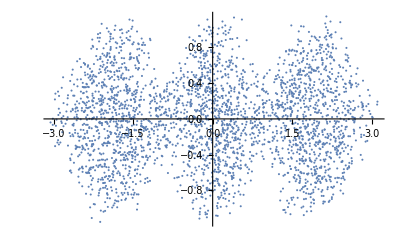

```mathematica
ListPlot[reduced]
```

```mathematica
reconstructed = dr[reduced, "OriginalVectors"];
```

```mathematica
ListPointPlot3D[{vectors, reconstructed}]
```

-Graphics3D-

```mathematica
dr = DimensionReduction[{{1, 2, 3}, {2, 3, 5}, {3, 5, 8}, {4, 5, 8.5}}]
```

DimensionReducerFunction[…]

```mathematica
newvectors = {{6, 7, Missing[]}, {5, Missing[], 11}};
dr[newvectors, "ImputedVectors"]
```

{{6.,7.,12.1769},{5.,6.49944,11.}}

```mathematica
dr = DimensionReduction[{-Graphics-, -Graphics-, -Graphics- , -Graphics-, -Graphics-, -Graphics-}, 5]
```

DimensionReducerFunction[…]

```mathematica
dr[{-Graphics-, -Graphics-, -Graphics- , -Graphics-, -Graphics-, -Graphics-}]
```

{{16.6901,0.66391,2.31437,8.67619,22.3044},{8.66663,12.1656,11.0589,15.3779,-16.1057},{23.1908,-8.59542,-12.001,-14.9865,-8.70455},{-14.2674,-21.1946,18.7505,-4.11292,-0.570139},{-19.8211,-4.78504,-22.4556,11.3487,-1.03039},{-14.459,21.7455,2.33289,-16.3034,4.10636}}

```mathematica
dr = DimensionReduction[{"the cat is grey", "what a nice dog", "here is a dog again"}]
```

DimensionReducerFunction[…]

```mathematica
dr=DimensionReduction[{DateObject[{2014,5,5,9,53,6.301579},"Instant","Gregorian",-6.],DateObject[{2000,1,1,0,0,0.},"Instant","Gregorian",-6.],DateObject[{2006,12},"Month","Gregorian",-6.],DateObject[{2007,8,23},"Day","Gregorian",-6.],DateObject[{2016,4,4,15,59,18.273754},"Instant","Gregorian",-4.]}]
```

DimensionReducerFunction[…]

```mathematica
dr[DateObject[{2003,1,2},"Day","Gregorian",-6.]]
```

{-1.81298,-0.13176}

```mathematica
dr = DimensionReduction[{{"the cat is grey", -Graphics-}, {"my cat is fast", -Graphics-}, {"this dog is scary", -Graphics-}, {"the big dog", -Graphics-}}]
```

DimensionReducerFunction[…]

```mathematica
dr[{"the nice cat", -Graphics-}]
```

{-50.569,-69.3081}

```mathematica
dr=DimensionReduction[{<|"age"->32,"height"->160,"gender"->"female"|>,<|"height"->183,"age"->41,"gender"->"female"|>,<|"height"->123,"age"->30,"gender"->"female"|>,<|"height"->175,"age"->21,"gender"->"male"|>,<|"height"->150,"age"->11,"gender"->"male"|>,<|"age"->52,"height"->164,"gender"->"female"|>}]
```

DimensionReducerFunction[…]

```mathematica
dr=DimensionReduction[{"The cat is grey.","My cat is fast.","This dog is scary.","The big dog."},FeatureExtractor->{ToUpperCase,RemoveDiacritics,"SegmentedWords"}]
```

```mathematica
dr = DimensionReduction[{{1, "A"}, {2, "A"}, {2, "B"}, {1, "B"}}]
```

DimensionReducerFunction[…]

```mathematica
dr[{{1, "A"}, {2, "A"}, {2, "B"}, {1, "B"}}] //MatrixForm
```

(-1.41421 | -1.
-1.41421 | 1.
1.41421 | 1.
1.41421 | -1.)

```mathematica
dr[{{1, "A"}, {2, "A"}, {2, "B"}, {1, "C"}}] //MatrixForm
```

(-1.41421 | -1.
-1.41421 | 1.
1.41421 | 1.
-2.22045×10^-16 | -1.)

```mathematica
iris = ExampleData[{"MachineLearning", "FisherIris"}, "Data"];
```

```mathematica
diris = DimensionReduction[iris[[All, 1]], 2, Method -> "TSNE"]
```

```mathematica
DimensionReducerFunction[…]
```

General::noinfo: Input expression DimensionReducerFunction[…] contains insufficient information to interpret the result.

```mathematica
byspecies=GroupBy[iris,Last->First];
```

```mathematica
diris=DimensionReduction[iris[[All,1]],2,Method->"TSNE"]
```

DimensionReducerFunction[…]

```mathematica
byspecies=GroupBy[iris,Last->First];
```

```mathematica
byspecies=diris/@byspecies;
```

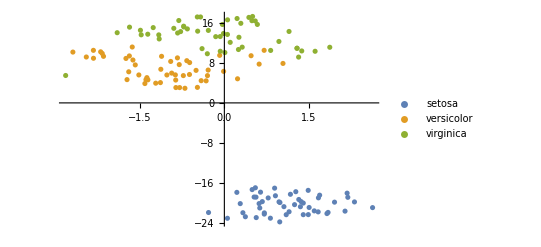

```mathematica
ListPlot[Values[byspecies], PlotLegends-> Keys[byspecies]]
```

```mathematica
diris = DimensionReduction[iris[[All, 1]], 2, Method -> {"TSNE", "Perplexity"->100}]
```

DimensionReducerFunction[…]

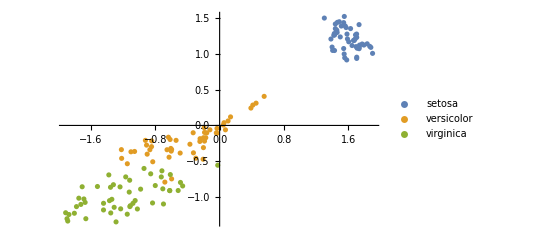

```mathematica
byspecies = GroupBy[iris, Last-> First];
byspecies = diris  /@ byspecies;
ListPlot[Values[byspecies], PlotLegends-> Keys[byspecies]]
```

```mathematica
digits = {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-};
```

```mathematica
dr = DimensionReduction[digits, 2, Method->"AutoEncoder"]
```

DimensionReducerFunction[…]

```mathematica
ListPlot[MapThread[Labeled[#1, #2]&,{dr[digits], digits}]]
```

-Graphics-

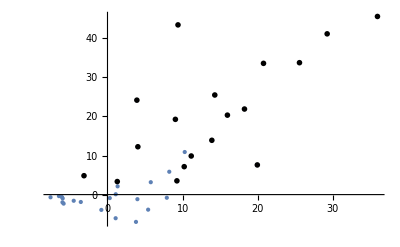

```mathematica
newdigits = {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-};
ListPlot[MapThread[Labeled[#1,Image[#2,ImageSize->15]]&,{dr[newdigits],newdigits}],PlotStyle->PointSize[Tiny]]
```

```mathematica
digits=ExampleData[{"MachineLearning","MNIST"},"TestData"][[All,1]]
```

```mathematica
RandomSample[digits, 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
digits = Flatten[ImageData[#]] &/@ RandomSample[digits];
```

```mathematica
trainingset=digits[[;;9000]];
testset=digits[[9001;;]];
```

```mathematica
Dimensions[trainingset]
```

{9000,784}

```mathematica
dr = DimensionReduce[trainingset, 50]
```

{{-4.64486,-3.51574,1.8053,9.62515,-11.8141,1.2237,1.48866,36,-0.569746,0.207086,0.393329,1.31787,0.209237,1.01474,0.683162},8998,{1}}
 |  |  |  |

```mathematica
vector = RandomChoice[testset];
dr[vector]
```

{1}[{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,710,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}]
 |  |  |  |

```mathematica
toimage = Image[Partition[#, 28], ImageSize -> Tiny] &;
```

```mathematica
toimage /@ {vector, dr[vector, "ReconstructedVectors"]}
```

Image::imgarray: The specified argument {{-4.64486,-3.51574,1.8053,9.62515,-11.8141,1.2237,1.48866,4.79957,«35»,-0.569746,0.207086,0.393329,1.31787,0.209237,1.01474,0.683162},«49»,«8950»}[] should be an array of rank 2 or 3 with machine-sized numbers.

{-Graphics-,Image[{{-4.64486,-3.51574,1.8053,9.62515,-11.8141,1.2237,38,0.207086,0.393329,1.31787,0.209237,1.01474,0.683162},8998,{1}}[],1]}
 |  |  |  |

```mathematica
toimage=Image[Partition[#,28],ImageSize->Tiny]&;
toimage/@{vector,dr[vector,"ReconstructedVectors"]}
```

Image::imgarray: The specified argument {{-4.64486,-3.51574,1.8053,9.62515,-11.8141,1.2237,1.48866,4.79957,«35»,-0.569746,0.207086,0.393329,1.31787,0.209237,1.01474,0.683162},«49»,«8950»}[] should be an array of rank 2 or 3 with machine-sized numbers.

{-Graphics-,Image[{{-4.64486,-3.51574,1.8053,9.62515,-11.8141,1.2237,38,0.207086,0.393329,1.31787,0.209237,1.01474,0.683162},8998,{1}}[],1]}
 |  |  |  |

```mathematica
ratings=SparseArray[Uncompress["1:eJztW9FOwzAMzLpVSPwF/wMvfAJCoL7AQ/l/0XUSGTRJ7fM5zSpeqq3qUse+nM9O9vDy+fz2GkIYT9PlcRi/3u5/fQvnb3fT5WkYx+HjfXFj6KfPy7vH6fN8QUdYsWM4WcbW3xgO54G0vjk/6m0pEi+aW/j2ZZyowJODzzrm2y9zgfB0zOJpNlE6Qrd4txCkJoRr45KZKGppmqfSo1E4MO18+LEVPhSOTQuV1WcZKHUGPF18sDM+jGseJaDoWE6MYPhT1hpMuBrTkTzvpz2c1hrNtUSMN7oGt+d3aT5TLMUrUjHjqQ9MgYRoI0eMC3grLb9iNjMRuMP6p4WKwp/VGWJn9nGrI5ImnhHfh+sF0A6eULYg+qbmNNrhC8S+269tCgm47no0VVbpu8uavaS3qQas4eYg8y8tLdNxk5EVtMIC7rcU0DR73bOv4plr1bOFtQJSj2s0v6oYoej/FnOqxgsS7cHbT5D1a80cE6UhD79p0/em0YSVtLDvLqkhFTJnLayi9ync+edSMMrJzzTitdYxmiAl9lnyQuoqrofsizAd1IUcu2k6WyJM0fhxs72+n3jXAeVm66WAinbWMM5jJklSSzdV1bbCOBZamXDgkf122HtpSz3j9c9VGl7wPDNAo5hCYF33b5rpYa0pPlVYd98fzRNnhdjF6pWX3nagC6RhQ1uSwt9JtYqHMU41r7Cv2mAdXiGfSJkSFQ2b9urUeEfPLMkgZrcPZKjGNIxUo8jmVW3NOp4Pl8o8y37U5cc+2kb6WJSpUo0ARys2wnpk3qZDgsnR8H5eOn2o3g3FvrDN4HKjHb3GOydI0wLGnjX3/wBa32RKUwVr3HaewvmXGzuchwonBts6J7jRWRUeaul+ct7lIJ3VTyf7reqk2j2dbwG5Z0c="],Automatic,Missing[]]
```

SparseArray[…]

```mathematica
ratings[[;;10,;;5]] //MatrixForm
```

(Missing[] | Missing[] | 5 | Missing[] | 3
Missing[] | 4 | Missing[] | Missing[] | 5
Missing[] | Missing[] | 4 | 4 | Missing[]
Missing[] | Missing[] | 5 | 5 | Missing[]
Missing[] | Missing[] | Missing[] | 4 | 3
Missing[] | Missing[] | 2 | 3 | Missing[]
Missing[] | Missing[] | 3 | 4 | Missing[]
4 | Missing[] | Missing[] | Missing[] | 4
4 | Missing[] | 4 | Missing[] | Missing[]
Missing[] | Missing[] | 5 | Missing[] | Missing[])

```mathematica
training = ratings[[;;80]];
```

```mathematica
test = ratings[[81;;]];
```

```mathematica
dr=DimensionReduction[training,3]
```

DimensionReducerFunction[…]

```mathematica
newuser = RandomChoice[test]
```

{Missing[],Missing[],Missing[],5,Missing[],2,Missing[],Missing[],Missing[],Missing[]}

```mathematica
dr[newuser, "ImputedVectors"]
```

{3.25362,2.35112,4.07189,5.,1.85173,2.,4.0673,2.64344,4.93623,2.79333}

```mathematica
dr = DimensionalReduction[dataset, 10]
```

DimensionalReduction[{{7.,0.27,0.36,20.7,0.045,45.,170.,1.001,3.,0.45,8.8}→6.,{6.3,0.3,0.34,1.6,0.049,14.,132.,0.994,3.3,0.49,9.5}→6.,4895,{6.,0.21,0.38,0.8,0.02,22.,98.,0.98941,3.26,0.32,11.8}→6.},10]
 |  |  |  |

```mathematica
nf = Nearest[dr[dataset]->Automatic]
```

Nearest::near1: DimensionalReduction[{{7.,0.27,0.36,20.7,0.045,45.,170.,1.001,3.,0.45,8.8}→6.,{6.3,0.3,0.34,1.6,0.049,14.,132.,0.994,3.3,0.49,9.5}→6.,{8.1,0.28,0.4,6.9,0.05,30.,97.,0.9951,3.26,0.44,10.1}→6.,«46»,{6.9,0.19,0.35,5.,0.067,32.,150.,0.995,3.36,0.48,9.8}→5.,«4848»},10][{«1»}]→Automatic is neither a list of real points nor a valid list of rules.

Nearest[DimensionalReduction[{{7.,0.27,0.36,20.7,0.045,45.,170.,1.001,3.,0.45,8.8}→6.,4896,{6.,0.21,0.38,0.8,0.02,22.,98.,0.98941,3.26,0.32,11.8}→6.},10][{{7.,0.27,0.36,20.7,0.045,45.,170.,1.001,3.,0.45,8.8}→6.,4896,{6.,0.21,7,0.32,11.8}→6.}]→9]
 |  |  |  |

```mathematica
nearestdog=dataset[[First@nf[dr[#]]]]&
```

dataset⟦First[nf[dr[#1]]]⟧&

```mathematica
nearestdog[-Graphics-]
```

Part::pkspec1: The expression … cannot be used as a part specification.

{{7.,0.27,0.36,20.7,0.045,45.,170.,1.001,3.,0.45,8.8}→6.,{6.3,0.3,0.34,1.6,0.049,14.,132.,0.994,3.3,0.49,9.5}→6.,4894,{5.5,0.29,0.3,1.1,0.022,20.,110.,0.98869,3.34,0.38,12.8}→7.,{6.,0.21,0.38,0.8,0.02,22.,98.,0.98941,3.26,0.32,11.8}→6.}⟦20[1]1-Graphics-]⟧
 |  |  |  |